```mathematica
(*Самая простая в реализации функция нахождения ближайших точек. Реализована двойным циклом. Сложность - O(n^2)*)
SimpleMinDistance[Ar_]:=Block[{im=1,jm=2,de=EuclideanDistance[Ar[[1]],Ar[[2]]]},
If[Length[Ar]<=1,Return[0](*если только один элемент в массиве или он пустой, то результат нулевой*),
For[i=1,i<Length[Ar],i++,
For[j=i+1,j≤Length[Ar],j++,
If[EuclideanDistance[Ar[[i]],Ar[[j]]]<EuclideanDistance[Ar[[im]],Ar[[jm]]],im=i(*индекс первой точки из двух самых близких*);jm=j(*индекс второй точки из двух самых близких*);de=EuclideanDistance[Ar[[i]],Ar[[j]](*минимальное евклидово расстояние*)]
]
]
];
Return[{de,{im,jm}}](*в результате возвращаем список, на первой позиции - расстояние, на второй позиции еще один список для индексов полученных вершин*)
]
];
```

```mathematica
(*возвращает индекс элемента массива, если таковой имеется*)
GetIndexByValue[A_,val_]:=Block[{},
For[i=1,i≤Length[A],i++,
If[A[[i]]==val,Return[i]]
];
Return[0];
];
```

```mathematica
(*Более сложный в реализации, но быстрый рекурсивный алгоритм. Сложность - O(n*log(n)). Очень подробно описан в книге Кормен "Алгоритмы. Построение и анализ. - 2013" стр.1086(у меня)*)
FastMinDistance[Ar_(*несортированное мн-во точек*),X_(*это же мн-во сортированное в порядке возрастания координаты Х*),Y_(*в порядке возрастания координаты Y*)]:=Block[{d,dl,dr,dk,im,jm,mid,Pl={},Pr={},Xl={},Xr={},Yl={},Yr={},Pcur={},Ycheck={}},
If[Length[Ar]≤3,Return[SimpleMinDistance[Ar](*если длина входящего массива не превышает 3, то работает алгоритм простого перебора*)],
(*Разделение*)
(*нужно разделить массив на 2 равные части. Поскольку у нас есть отсортированный по Х массив сделать это очень просто*)
mid=X[[IntegerPart[(Length[X]+1)/2](*берем элемент с индексом равным половине длины массива с округлением в большую сторону*),1(*берем Ховую координату*)]];
(*теперь нужно разбить исходный массив на два подмассива, а точнее сортированные части X, Y тоже нужно разбить на 2 части с сохранением порядка сортированных элементов*)
For[i=1,i≤Length[Ar],i++,
Which[
(*подробно опишу разбиение несортированного списка(2 остальных по аналогии)*)
Ar[[i,1]]==mid,(*средняя точка должна попасть в оба подмассива, поэтому если ее Ховая координата равна среней, то такая точка войдет в оба из них*)
Pl=Append[Pl,Ar[[i]]];
Pr=Append[Pr,Ar[[i]]],
Ar[[i,1]]<mid,(*если ее Ховая координата меньше среней, то есть левее, то такая точка войдет левый подмассив*)
Pl=Append[Pl,Ar[[i]]],
Ar[[i,1]]>mid,(*обратно -> в правый*)
Pr=Append[Pr,Ar[[i]]]
];
Which[
Y[[i,1]]==mid,
Yl=Append[Yl,Y[[i]]];
Yr=Append[Yr,Y[[i]]],
Y[[i,1]]≤mid,
Yl=Append[Yl,Y[[i]]],
Y[[i,1]]≥mid,
Yr=Append[Yr,Y[[i]]]
];
Which[
X[[i,1]]==mid,
Xl=Append[Xl,X[[i]]];
Xr=Append[Xr,X[[i]]],
X[[i,1]]≤mid,
Xl=Append[Xl,X[[i]]],
X[[i,1]]≥mid,
Xr=Append[Xr,X[[i]]]
]
];
(*Властвование*)
(*для каждого из 2ух подмассивов делается свой рекурсивный вызов*)
dl=FastMinDistance[Pl,Xl,Yl];
dr=FastMinDistance[Pr,Xr,Yr];
(*поскольку в результате постоянного деления множества на все более мелкие подмножества,в итоге произойдет вызов функции SimpleMinDistance и эти переменные будут иметь вид: {расстояние,{индекс, индекс}}. При чем индексы получатся совершенно левые и ненужные, потому что при вызове пойдет массив типа Pl или Pr, индексация в котором отлична от основного Ar*)
If[dl[[1]]<dr[[1]](*в переменную d войдет минимальное из 2ух расстояний*),d=dl;Pcur=Pl(*в Pcur мы заносим массив из которого получилось минимальное расстояние. Он пригодиться потом когда будем восстанавливать индексацию*),d=dr;Pcur=Pr];
(*Комбинирование*)
(*на тот случай если минимальное расстояние на самом деле получается не в каком то из двух подмассивов, а между ними(одна точка в одном, другая в другом)*)
For[i=1,i≤Length[Y],i++,(*составляем список всех вершин, расположенных в порядке возрастания по Y и не более чем на расстоянии d от средней линии*)
If[Abs[mid-Y[[i,1]]]≤d[[1]](*первый элемент d - это расстояние*),Ycheck=Append[Ycheck,Y[[i]]]]
];
If[Length[Ycheck]>2,(*если в массив Ycheck попала одна точка, то это средняя. Если 2, то это средняя и еще какая-то. Поскольку средняя лежит в обоих подмассивах, а "какая-то" в одном из них то нет смысла проверять, поскольку эта проверка была сделана в предыдущем шаге*)
dk=SimpleMinDistance[Ycheck];(*если их больше то находим минимальное среди них расстояние*)
If[dk[[1]]<d[[1]],d=dk;Pcur=Ycheck](*сравниваем это с минимальным из двух подмассивов. Берем меньшее*)
];
(*все что осталось - это восстановить индексацию исходного массива Ar*)
Return[{d[[1]],{GetIndexByValue[Ar(*ищем индекс в Ar*),Pcur[[d[[2(*рассматриваем индексы*),1(*берем первый из них*)]] ]] ](*по значению, из подмассива в котором было найдено минимальное расстояние*),GetIndexByValue[Ar,Pcur[[d[[2,2(*теперь второй индекс*)]] ]] ]}}]
]
];
```

{31,34}

{31,34}

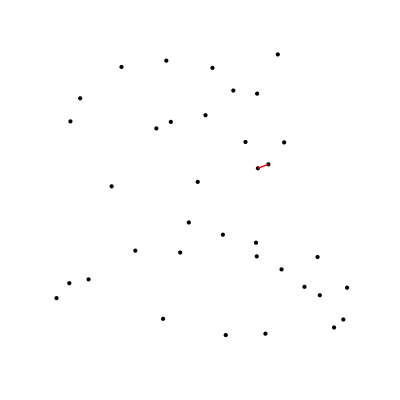

```mathematica
A=Table[{RandomReal[100],RandomReal[100]},{36}];
X=SortBy[A,First];
Y=SortBy[A,Last];
(*если элементы массива имеют вид {Subscript[a, i],Subscript[b, i]}, то SortBy[ _ ,First] означает что сортируем в порядке возрастания подэлементов Subscript[a, i]. А SortBy[ _ ,Last] соответственно по Subscript[b, i]*)
{u,v}=SimpleMinDistance[A][[2]](*в качестве проверки правильности быстрого алгоритма можно сделать вызов медленного, но однозначно правильного*)
{x,y}=FastMinDistance[A,X,Y][[2]](*берем вторую часть, потому что нас в данной ситуации не интересует само расстояние, а скорее индексы элементов*)
Graphics[{Point[A],Red,Line[{A[[x]],A[[y]]}]},PlotRange->{{-5,105},{-5,105}}]
```